```mathematica
(*_________________________________________________________________________________________________________________________________________________________________________________*)
(* Twin Boundary for T-O Interface *)
Clear["`*"]
Clear["u1", "u2", "u3", "u4", "u5", "u6"];
Clear["a1", "a11","a12","a111","a112","a123","a1111","a1112","a1122","a1123"];
Clear["Q11", "Q12", "Q44", "A11", "A12", "Po"];
Symbol[ "a1"]Symbol[ "a11"]Symbol[ "a12"]Symbol[ "a111"]Symbol[ "a112"]Symbol[ "a123"]Symbol[ "a1111"]Symbol[ "a1112"]Symbol[ "a1122"]Symbol["a1123"];
Symbol["u1"]Symbol[ "u2"]Symbol["u3"]Symbol["u4"]Symbol[ "u5"]Symbol[ "u6"];
Symbol["Q11"] Symbol["Q12"] Symbol["Q44"]Symbol["A11"] Symbol["A12"];
"Summation Notation"
(* The Free Energy in Summation Notation *)
(* FPolarSum[P_]=Subscript[a,1](Sum[Subscript[P,i]^2, i])  +Subscript[a,11](Sum[Subscript[P,i]^4,i])+Subscript[a,12](Sum[Subscript[P,i]^2*Subscript[P,j]^2, i<j])
FElectrostrictionSum[P_,u_]=-Subscript[q,11]*Sum[Subscript[u,ii]Subscript[P,i]^2, i]-Subscript[q,12]*Sum[Subscript[u,ii]*(Subscript[P,j]^2+Subscript[P,k]^2), i≠j≠k]-Subscript[q,44]*Sum[Subscript[u,ij]*Subscript[P,i]*Subscript[P,j],i<j]
FElasticSum[u_]=1/2*Subscript[c,11]*Sum[Subscript[u,i]^2 ,i]+Subscript[c,12]*Sum[Subscript[u,ii]*Subscript[u,j j], i<j]+1/2*Subscript[c,44]*Sum[Subscript[u,ij],i j]/.Subscript[u,i]-> Subscript[u,ii]
FGradientSum[P_]=Subscript[g,11]/2*Sum[Subscript[P, i,i]^2, i]+Subscript[g,12]*Sum[Subscript[P,i,i]Subscript[P,j,j], i<j]+Subscript[g,44]/2*Sum[(Subscript[P,i,j]+Subscript[P,j,i])^2, i<j]  *)
```

Summation Notation

```mathematica
(*______________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________________*)
(* TENSOR NOTATION *)
Symbol["P1"] Symbol["P2"] Symbol["P3"];

FPolar[P_]=Subscript[a,1](Sum[Subscript[P,i]^2, {i,1,3}])  +Subscript[a,11](Sum[Subscript[P,i]^4,{i,1,3}])+Subscript[a,12](Sum[Subscript[P,i]^2*Subscript[P,j]^2, {j,1,3}, {i,1,j-1}]) +
Subscript[a,111](Sum[Subscript[P,i]^6, {i,1,3}])+1/2*Simplify[Subscript[a,112](Sum[Subscript[P,i]^2*(Subscript[P,j]^4+Subscript[P,k]^4)(Boole[i≠j]&&Boole[i≠k]&&Boole[j≠k]),{i,1,3} ,{j,1,3}, {k,1,3}])]+Subscript[a,123](Sum[Subscript[P,i]^2Subscript[P,j]^2Subscript[P,k]^2, {i,1,3},{j,1,i-1},{k,1,j-1}])/.{False->0, True->1};
FElectrostriction[P_,u_]=-Subscript[q,11]*Sum[Subscript[u,i,i]Subscript[P,i]^2, {i,1,3}]-1/2Simplify[Subscript[q,12]*Sum[Subscript[u,i,i](Subscript[P,j]^2+Subscript[P,k]^2)( Boole[i≠j]&&Boole[i≠k]&&Boole[j≠k]),{i,1,3},{j,1,3},{k,1,3}]]-Subscript[q,44]*Sum[Subscript[u,i,j]*Subscript[P,i]*Subscript[P,j],{j,1,3}, {i,1,j-1}]/.{False->0, True->1}/.{Subscript[u,1,1]-> Subscript[u,1],Subscript[u,2,2]-> Subscript[u,2],Subscript[u,3,3]-> Subscript[u,3],Subscript[u,2,3]-> Subscript[u,4],Subscript[u,1,3]-> Subscript[u,5],Subscript[u,1,2]-> Subscript[u,6]}
FElastic[u_]=1/2*Subscript[c,11]*Sum[Subscript[u,i,i]^2 ,{i,1,3}]+Subscript[c,12]*Sum[Subscript[u,i,i]*Subscript[u,j ,j], {j,1,3}, {i,1,j-1}]+1/2*Subscript[c,44]*Sum[Subscript[u,i,j]^2,{j,1,3},{i,1,j-1}]/.{Subscript[u,1,1]-> Subscript[u,1],Subscript[u,2,2]-> Subscript[u,2],Subscript[u,3,3]-> Subscript[u,3],Subscript[u,2,3]-> Subscript[u,4],Subscript[u,1,3]-> Subscript[u,5],Subscript[u,1,2]-> Subscript[u,6]};
FGradient[P_]=Subscript[g,11]/2*Sum[Subscript[P, i,i]^2, {i,1,3}]+Subscript[g,12]*Sum[Subscript[P,i,i]Subscript[P,j,j],{j,1,3},{i,1,j-1}]+Subscript[g,44]/2*Sum[(Subscript[P,i,j]+Subscript[P,j,i])^2, {j,1,3},{i,1,j-1}];
FBulk[P_,u_]=FPolar[P]+FElectrostriction[P, u]+FElastic[u] (*+FGradient[P]; *)
```

-q_11 (P_1^2 u_1+P_2^2 u_2+P_3^2 u_3)-q_12 (P_3^2 (u_1+u_2)+P_2^2 (u_1+u_3)+P_1^2 (u_2+u_3))-q_44 (P_2 P_3 u_4+P_1 P_3 u_5+P_1 P_2 u_6)

a_123 P_1^2 P_2^2 P_3^2+a_1 (P_1^2+P_2^2+P_3^2)+a_12 (P_1^2 P_2^2+P_1^2 P_3^2+P_2^2 P_3^2)+a_11 (P_1^4+P_2^4+P_3^4)+a_111 (P_1^6+P_2^6+P_3^6)+a_112 (P_1^4 (P_2^2+P_3^2)+P_2^2 P_3^2 (P_2^2+P_3^2)+P_1^2 (P_2^4+P_3^4))-q_11 (P_1^2 u_1+P_2^2 u_2+P_3^2 u_3)+c_12 (u_1 u_2+u_1 u_3+u_2 u_3)+1/2 c_11 (u_1^2+u_2^2+u_3^2)-q_12 (P_3^2 (u_1+u_2)+P_2^2 (u_1+u_3)+P_1^2 (u_2+u_3))-q_44 (P_2 P_3 u_4+P_1 P_3 u_5+P_1 P_2 u_6)+1/2 c_44 (u_4^2+u_5^2+u_6^2)

```mathematica
(*___________________________________________________________________________________________________________________________________________________________________________________*)
(* New Rules Functions to take Derivatives of subscripted notations. *)
SubToVariableRules={Subscript[P, 1,1]-> PG11,Subscript[P, 1,2]-> PG12, Subscript[P, 1,3]-> PG13, Subscript[P, 2,2]-> PG22, Subscript[P, 2,1]-> PG21, Subscript[P, 3,1]-> PG31, Subscript[P, 2,3]-> PG23, Subscript[P, 3,2]-> PG32, Subscript[P, 3,3]-> PG33,Subscript[P, 1] -> P1, Subscript[P, 2] -> P2,Subscript[P, 3] -> P3,
Subscript[u, 1]-> u1,Subscript[u, 2]-> u2,Subscript[u, 3]-> u3,Subscript[u, 4]-> u4,Subscript[u, 5]-> u5,Subscript[u, 6]-> u6};
VariableToSubRules={ PG11-> Subscript[P, 1,1],PG12-> Subscript[P, 1,2],PG13-> Subscript[P, 1,3],PG22-> Subscript[P, 2,2],PG21-> Subscript[P, 2,1],PG31-> Subscript[P, 3,1],PG23-> Subscript[P, 2,3],PG32-> Subscript[P, 3,2],PG33-> Subscript[P, 3,3],P1-> Subscript[P, 1],P2-> Subscript[P, 2],P3-> Subscript[P, 3],
u1-> Subscript[u, 1],u2-> Subscript[u, 2],u3-> Subscript[u, 3],u4-> Subscript[u, 4],u5-> Subscript[u, 5],u6-> Subscript[u, 6]};
CoefficientsToVariables={A11->-((-2 Subscript[a, 11] (Subscript[c, 11]^2+Subscript[c, 11] Subscript[c, 12]-2 Subscript[c, 12]^2)+Subscript[c, 12] Subscript[q, 11] (Subscript[q, 11]-8 Subscript[q, 12])+Subscript[c, 11] (Subscript[q, 11]^2+8 Subscript[q, 12]^2))/(2 (Subscript[c, 11]-Subscript[c, 12]) (Subscript[c, 11]+2 Subscript[c, 12]))),A12->(2 Subscript[a, 12] (Subscript[c, 11]^2+Subscript[c, 11] Subscript[c, 12]-2 Subscript[c, 12]^2) Subscript[c, 44]+2 Subscript[c, 12]^2 Subscript[q, 44]^2+Subscript[c, 12] (2 Subscript[c, 44] (Subscript[q, 11]^2+8 Subscript[q, 12]^2)-Subscript[c, 11] Subscript[q, 44]^2)-Subscript[c, 11] (8 Subscript[c, 44] Subscript[q, 12] (Subscript[q, 11]+Subscript[q, 12])+Subscript[c, 11] Subscript[q, 44]^2))/(2 (Subscript[c, 11]-Subscript[c, 12]) (Subscript[c, 11]+2 Subscript[c, 12]) Subscript[c, 44]),
Subscript[a, 1]->a1,Subscript[a, 11]->a11, Subscript[a, 12]->a12,Subscript[a, 111]->a111,Subscript[a, 112]->a112,Subscript[a, 123]->a123,
Subscript[a, 1111]->a1111,Subscript[a, 1112]->a1112,Subscript[a, 1122]->a1122,Subscript[a, 1123]->a1123,
Subscript[c, 11]->c11,Subscript[c, 12]->c12,Subscript[c, 44]->c44,Subscript[q, 11]->q11,Subscript[q, 12]->q12,Subscript[q, 44]->q44};
ElectrostrictiveCoefficients={(-c12 q11+2 c11 q12)/(c11^2+c11 c12-2 c12^2)-> Q12, (c11 q11+c12 q11-4 c12 q12)/(c11^2+c11 c12-2 c12^2)-> Q11, q44/c44-> Q44};


(* Wang Et al. Coefficients and Elastic Constants *)
ThermodynamicCoefficients={ a1->3.61*10^5*(T-391),a11->-1.83*10^9+4*10^6*T,a12->-2.24*10^9+6.7*10^6*T,a111->1.39*10^10-3.2*10^7*T,a112->-2.2*10^9,a123->5.51*10^10,
a1111->4.84*10^10,a1112->2.53*10^11,a1122->2.80*10^11,a1123->9.35*10^10, Q11->14.20*10^9,Q12->-0.74*10^9,Q44->1.57*10^9};
TElasticConstants={c11-> 300*10^9,c12->109*10^9};
OElasticConstants={c11->150*10^9,c22->312*10^9,c33->150*10^9,c44->135*10^9,c12->100*10^9};
LiCoefficients={a1-> 4.124*10^5*(T-388),a11-> -2.097*10^8,a12->7.974*10^8,a111-> 1.294*10^9,a112-> -1.95*10^9,a123->-2.5*10^9, q11->14.20*10^9,q12->-0.74*10^9,q44->1.57*10^9};
BellCoefficients={a1->3.34*10^5*(T-381),a11->4.69*10^6*(T-393)-2.02*10^8,a12->-3.23*10^8,a111->-5.52*10^7*(T-393)+2.76*10^9,a112->4.47*10^9,a123->4.91*10^9, a1111->3.863*10^10,
c11->27.50*10^10,c12->17.90*10^10,c44->5.43*10^10, q11->14.20*10^9,q12->-0.74*10^9,q44->1.57*10^9};
Renormalization={A11->Subscript[a, 11]-1/2*((c11 q11+c12 q11-2 c12 q12) Subscript[q, 11])/(c11^2+c11 c12-2 c12^2)-((-c12 q11+c11 q12) Subscript[q, 12])/((c11-c12) (c11+2 c12))};
ElectrostrictiveCoefficients={(-c12 q11+2 c11 q12)/(c11^2+c11 c12-2 c12^2)-> Q12, (c11 q11+c12 q11-4 c12 q12)/(c11^2+c11 c12-2 c12^2)-> Q11, q44/c44-> Q44};
Rules
```

Rules

```mathematica
(*___________________________________________________________________________________________________________________________________________________________________________________*)
(* Determining equilibrium solutions for the strain *)
FStrainDerivative[P_,u_]={Collect[D[FBulk[P,u]/.SubToVariableRules, u1], u1, Simplify],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u2]], u2],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u3]], u3],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u4]], u4], Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u5]], u5],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u6]], u6]}/.CoefficientsToVariables/.ElectrostrictiveCoefficients;

StrainSolutions=Collect[Solve[{(FStrainDerivative[P,u][[1]])==0,(FStrainDerivative[P,u][[2]])==0,
(FStrainDerivative[P,u][[3]])==0,(FStrainDerivative[P,u][[4]])==0,
(FStrainDerivative[P,u][[5]])==0,(FStrainDerivative[P,u][[6]])==0},{u1,u2,u3, u4,u5,u6}], {P1,P2,P3},Simplify]/.ElectrostrictiveCoefficients

StrainSolutionSimplified={{u1->P1^2*Q11+Q12*(P2^2+P3^2), u2->P2^2 Q11+(P1^2+P3^2) Q12, u3->P3^2 Q11+(P1^2+P2^2) Q12, u4->P2 P3 Q44,u5->P1 P3 Q44,u6->P1 P2 Q44}}



(* Renormalization *)
Collect[D[FBulk[P,u]/.SubToVariableRules, P3]/.StrainSolutionSimplified//.P2->0,{P1,P3}]

1/2(Q11 Subscript[q, 11])+Q12 Subscript[q, 12]/.CoefficientsToVariables/.BellCoefficients/.{Q11->0.11,Q12->-0.034}



FBulkP3Renormalized=2 P3 Subscript[a, 1]+6 P3^5 Subscript[a, 111]+4A11 P3^3 ;
```

{{u1→(P2^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P3^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P1^2 (c11 q11+c12 q11-2 c12 q12))/(c11^2+c11 c12-2 c12^2),u2→(P1^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P3^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P2^2 (c11 q11+c12 q11-2 c12 q12))/(c11^2+c11 c12-2 c12^2),u3→(P1^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P2^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P3^2 (c11 q11+c12 q11-2 c12 q12))/(c11^2+c11 c12-2 c12^2),u4→P2 P3 Q44,u5→P1 P3 Q44,u6→P1 P2 Q44}}

{{u1→P1^2 Q11+(P2^2+P3^2) Q12,u2→P2^2 Q11+(P1^2+P3^2) Q12,u3→P3^2 Q11+(P1^2+P2^2) Q12,u4→P2 P3 Q44,u5→P1 P3 Q44,u6→P1 P2 Q44}}

{2 P3 a_1+6 P3^5 a_111+2 P1^4 P3 a_112+P3^3 (4 a_11-2 Q11 q_11-4 Q12 q_12)+P1^2 (4 P3^3 a_112+P3 (2 a_12-2 Q12 q_11-2 Q11 q_12-2 Q12 q_12-Q44 q_44))}

8.0616×10^8

```mathematica
(*___________________________________________________________________________________________________________________________________________________________________________________*)
(* Determining the Equilibrium Solutions for the Polarization vector for Each Phase  *)

Collect[D[FBulk[P,u]/.SubToVariableRules, P3]/.P2-> 0/.P1-> 0/.StrainSolutions/.P1->0/.P2-> 0,P3];
(* Solve[%==0, P3]/.StrainSolutions; *)
Solve[(D[FPolar[P]/.SubToVariableRules, P3]/.P1->0/.P2->0)==0, P3];
FPolarRenormalized=2 P3 Subscript[a,1]+6 P3^5 Subscript[a,111]+4P3^3 (Subscript[A,11]);
Simplify[Solve[FPolarRenormalized==0, P3]];
Simplify[Series[Simplify[(√((-Subscript[A, 11]+√(Subscript[A, 11]^2-3 Subscript[a, 1] Subscript[a, 111]))/(3 Subscript[a, 111]))-√((-Subscript[a, 11]+√(Subscript[a, 11]^2-3 Subscript[a, 1] Subscript[a, 111]))/(3 Subscript[a, 111])))/.Subscript[A, 11]-> (Subscript[a, 11]-δA)], {δA, 0,2}]];
```

{{P3→0},{P3→-(√(-(A_11+√(-3 a_1 a_111+A_11^2))/a_111))/(√3)},{P3→(√(-(A_11+√(-3 a_1 a_111+A_11^2))/a_111))/(√3)},{P3→-(√((-A_11+√(-3 a_1 a_111+A_11^2))/a_111))/(√3)},{P3→(√((-A_11+√(-3 a_1 a_111+A_11^2))/a_111))/(√3)}}

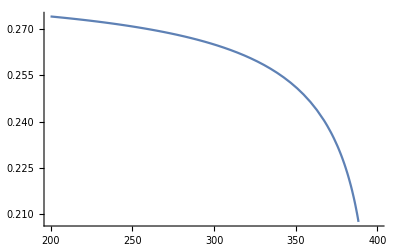

```mathematica
(* Strain-Independent Tetragonal Case *)
(*TSolution=Simplify[Solve[0==D[FPolar[P]/.SubToVariableRules, P3]/.P1->0/.P2->0, P3]]
(* Plot[{P3/.TSolution[[3]],P3/.TSolution[[4]],P3/.TSolution[[5]],P3/.TSolution[[6]]},{T,200,400}]; *)
PTSolutionswithoutStrain=Simplify[Solve[0==TSolution/.SubToVariableRules/.P1->0/.P2->0, P3]] *)

(* Strain-Dependent Tetragonal Phase *)
PTSolutions=Simplify[Solve[(FPolarRenormalized==0) , P3]//.CoefficientsToVariables/.ThermodynamicCoefficients/.TElasticConstants]; 
(* Plot[{P3/.PTSolutions[[2]],P3/.PTSolutions[[3]],P3/.PTSolutions[[4]],P3/.PTSolutions[[5]]},{T,200,400}]; *)
PTSolutionswithStrain=Simplify[Solve[(FPolarRenormalized==0) , P3]]
PTetragonalwithoutStrain=√((-Subscript[a, 11]+√(Subscript[a, 11]^2-3 Subscript[a, 1] Subscript[a, 111]))/(3 Subscript[a, 111]));
PTetragonal=√((-A11+√(A11^2-3 Subscript[a, 1] Subscript[a, 111]))/(3 Subscript[a, 111]));

Plot[{PTetragonalwithoutStrain/.CoefficientsToVariables/.BellCoefficients, PTetragonal/.CoefficientsToVariables/.BellCoefficients}, {T, 200,400}]
```

```mathematica
(* For the Orthorhombic Phase *)
P=.
FPolarizationDerivativeRenormalized[P_]={Collect[Simplify[D[FBulkRenormalized[P]/.SubToVariableRules, P1]], P1],
Collect[Simplify[D[FBulkRenormalized[P]/.SubToVariableRules, P2]], P2],
Collect[Simplify[D[FBulkRenormalized[P]/.SubToVariableRules, P3]], P3]};

Collect[D[FBulk[P,u]/.SubToVariableRules, P3]/.P2-> 0/.StrainSolutions/.P2-> 0,{P1,P3}]


POrthorhombic=√(-A11/(3 (Subscript[a, 111]+Subscript[a, 112]))-A12/(6 (Subscript[a, 111]+Subscript[a, 112]))+(√((2 A11+A12)^2-4 Subscript[a, 1] (3 Subscript[a, 111]+3 Subscript[a, 112])))/(6 (Subscript[a, 111]+Subscript[a, 112])));

Collect[Simplify[StrainSolutions/.{P1-> P/2^(1/2), P3-> P/2^(1/2)}/.P-> POrthorhombic],P]/.{A11-> Subscript[a',11],A12-> Subscript[a',12]};
OStrain=Simplify[StrainSolutions/.{P1-> P/2^(1/2), P3-> P/2^(1/2)}/.P-> POrthorhombic]//.CoefficientsToVariables/.ThermodynamicCoefficients/.OElasticConstants;

Plot[{ u3/.OStrain[[1,3]],u2/.OStrain[[1,2]], u5/.OStrain[[1,5]]}, {T, 200,400}, PlotLegends->{"u_1[T]=u_3[T]","u_2[T]", "u_5[T]"}, AxesLabel->{"Temperature (°K)", "Elastic Strain"}, PlotLabel->"Elastic Strain for the Orthorhombic Phase"];
```

{2 P3 a_1+6 P3^5 a_111+2 P1^4 P3 a_112+P3^3 (4 a_11-(2 (c11 q11+c12 q11-2 c12 q12) q_11)/(c11^2+c11 c12-2 c12^2)-(4 (-c12 q11+c11 q12) q_12)/((c11-c12) (c11+2 c12)))+P1^2 (4 P3^3 a_112+P3 (2 a_12-(2 (-c12 q11+c11 q12) q_11)/((c11-c12) (c11+2 c12))-(2 (-c12 q11+c11 q12) q_12)/((c11-c12) (c11+2 c12))-(2 (c11 q11+c12 q11-2 c12 q12) q_12)/(c11^2+c11 c12-2 c12^2)-Q44 q_44))}

```mathematica
(* For the Monoclinic Phase *)
PMcSolutions=Drop[Simplify[Solve[{(FPolarizationDerivativeRenormalized[P][[1]]==0)/.P2-> 0,
(FPolarizationDerivativeRenormalized[P][[3]]==0)/.P2-> 0,P1≠0,P3≠0, P1≠P3} , {P1,P3}]/.VariableToSubRules],-4];
%/.√(3 Subscript[a, 111]-Subscript[a, 112]) √(-36 Subscript[a, 1] Subscript[a, 111]^2-Subscript[a, 112] (20 A11^2-12 A11 A12+A12^2+4 Subscript[a, 1] Subscript[a, 112])+3 Subscript[a, 111] (4 A11^2+4 A11 A12-3 A12^2+8 Subscript[a, 1] Subscript[a, 112]))->B/.(-6 A11+3 A12) Subscript[a, 111]+2 A11 Subscript[a, 112]-A12 Subscript[a, 112]->C;

(* The final four solutions coincide with the Orthorhombic symmetry *)
P1Monoclinic=1/(√2)(√(1/(-3 Subscript[a, 111]+Subscript[a, 112])^2(C+√(3 Subscript[a, 111]-Subscript[a, 112]) √(-36 Subscript[a, 1] Subscript[a, 111]^2-Subscript[a, 112] (20 A11^2-12 A11 A12+A12^2+4 Subscript[a, 1] Subscript[a, 112])+3 Subscript[a, 111] (4 A11^2+4 A11 A12-3 A12^2+8 Subscript[a, 1] Subscript[a, 112])))))/.C-> ((-6 A11+3 A12) Subscript[a, 111]+2 A11 Subscript[a, 112]-A12 Subscript[a, 112]);
P3Monoclinic=1/(√(6 Subscript[a, 111]-2 Subscript[a, 112]))(√(1/(3 Subscript[a, 111]-Subscript[a, 112])(C+√(3 Subscript[a, 111]-Subscript[a, 112]) √(-36 Subscript[a, 1] Subscript[a, 111]^2-Subscript[a, 112] (20 A11^2-12 A11 A12+A12^2+4 Subscript[a, 1] Subscript[a, 112])+3 Subscript[a, 111] (4 A11^2+4 A11 A12-3 A12^2+8 Subscript[a, 1] Subscript[a, 112])))))/.C-> ((-6 A11+3 A12) Subscript[a, 111]+2 A11 Subscript[a, 112]-A12 Subscript[a, 112]);

Simplify[StrainSolutions/.P2-> 0/.P1-> P1Monoclinic/.P3->P3Monoclinic]/.{A11-> Subscript[a',11],A12-> Subscript[a',12]}

Collect[Simplify[StrainSolutions/.{P1-> P/2^(1/2), P3-> P/2^(1/2)}/.P-> POrthorhombic],P]/.{A11-> Subscript[a',11],A12-> Subscript[a',12]};
McStrain=Simplify[StrainSolutions/.P2-> 0/.P1-> P1Monoclinic/.P3->P3Monoclinic]//.CoefficientsToVariables/.ThermodynamicCoefficients/.OElasticConstants;

Plot[{u1/.McStrain[[1,1]], u2/.McStrain[[1,2]], u5/.McStrain[[1,5]]}, {T, 200,400}, PlotLegends->{"u_1[T] = u_3[T]","u_2[T]", "u_5[T]"}, AxesLabel->{"Temperature (°K)", "Elastic Strain"}, PlotLabel->"Elastic Strain for the Monoclinic Phase"];

(* Determining the real conditions of the polarization solutions for each phase
Simplify[(PTSolutions//.CoefficientsToVariables/.ThermodynamicCoefficients/.T-> 373)]
Simplify[POSolutions//.CoefficientsToVariables/.ThermodynamicCoefficients/.T-> 283]
Simplify[PMcSolutions//.CoefficientsToVariables/.ThermodynamicCoefficients/.T-> 283] *)
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

Drop::drop: Cannot drop positions -4 through -1 in {{}}.

{{u1→((-2 c12 q12+c11 (q11+q12)) (2 a_112 a'_11-a_112 a'_12+a_111 (-6 a'_11+3 a'_12)+√(3 a_111-a_112) √(-36 a_1 a_111^2+3 a_111 (8 a_1 a_112+4 (a')_11^2+4 a'_11 a'_12-3 (a')_12^2)-a_112 (4 a_1 a_112+20 (a')_11^2-12 a'_11 a'_12+(a')_12^2))))/(2 (c11-c12) (c11+2 c12) (-3 a_111+a_112)^2),u2→-((c12 q11-c11 q12) (2 a_112 a'_11-a_112 a'_12+a_111 (-6 a'_11+3 a'_12)+√(3 a_111-a_112) √(-36 a_1 a_111^2+3 a_111 (8 a_1 a_112+4 (a')_11^2+4 a'_11 a'_12-3 (a')_12^2)-a_112 (4 a_1 a_112+20 (a')_11^2-12 a'_11 a'_12+(a')_12^2))))/((c11-c12) (c11+2 c12) (-3 a_111+a_112)^2),u3→((-2 c12 q12+c11 (q11+q12)) (2 a_112 a'_11-a_112 a'_12+a_111 (-6 a'_11+3 a'_12)+√(3 a_111-a_112) √(-36 a_1 a_111^2+3 a_111 (8 a_1 a_112+4 (a')_11^2+4 a'_11 a'_12-3 (a')_12^2)-a_112 (4 a_1 a_112+20 (a')_11^2-12 a'_11 a'_12+(a')_12^2))))/(2 (c11-c12) (c11+2 c12) (-3 a_111+a_112)^2),u4→0,u5→1/(2 √(3 a_111-a_112))Q44 √((2 a_112 a'_11-a_112 a'_12+a_111 (-6 a'_11+3 a'_12)+√(3 a_111-a_112) √(-36 a_1 a_111^2+3 a_111 (8 a_1 a_112+4 (a')_11^2+4 a'_11 a'_12-3 (a')_12^2)-a_112 (4 a_1 a_112+20 (a')_11^2-12 a'_11 a'_12+(a')_12^2)))/(3 a_111-a_112)) √((2 a_112 a'_11-a_112 a'_12+a_111 (-6 a'_11+3 a'_12)+√(3 a_111-a_112) √(-36 a_1 a_111^2+3 a_111 (8 a_1 a_112+4 (a')_11^2+4 a'_11 a'_12-3 (a')_12^2)-a_112 (4 a_1 a_112+20 (a')_11^2-12 a'_11 a'_12+(a')_12^2)))/(-3 a_111+a_112)^2),u6→0}}

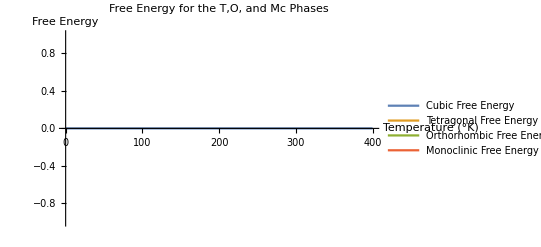

```mathematica
(*___________________________________________________________________________________________________________________________________________________________________________________*)
(* Inserting the polarization solutions into the free energy for each respective phase determines the most stable phase (i.e. the phase with the lowest free energy) *)

(* For the Tetragonal Phase *)
FTetragonal=Simplify[(FBulkRenormalized[P]-FGradient[P])/.SubToVariableRules]/.{P1->0,P2->0,P3->PTetragonal}/.VariableToSubRules;
(* For the Orthorhombic Phase *)
FOrthorhombic=Simplify[(FBulkRenormalized[P]-FGradient[P])/.SubToVariableRules]/.
{P1->POrthorhombic/2^(1/2),P2->0,P3->POrthorhombic/2^(1/2)}/.VariableToSubRules;
(* For the Monoclinic Phase *)
FMonoclinic=Simplify[(FBulkRenormalized[P]-FGradient[P])/.SubToVariableRules]/.
{P1->P1Monoclinic,P2->0,P3->P3Monoclinic}/.VariableToSubRules;

FinalFreeEnergies={Simplify[(FTetragonal//.CoefficientsToVariables/.ThermodynamicCoefficients)],
Simplify[(FOrthorhombic//.CoefficientsToVariables/.ThermodynamicCoefficients)],
Simplify[(FMonoclinic//.CoefficientsToVariables/.ThermodynamicCoefficients)]};
Plot[{0*T,FinalFreeEnergies[[1]],FinalFreeEnergies[[2]],FinalFreeEnergies[[3]]} ,{T, 0,400}, PlotLegends->{"Cubic Free Energy","Tetragonal Free Energy","Orthorhombic Free Energy","Monoclinic Free Energy" }, AxesLabel->{"Temperature (°K)", "Free Energy"}, PlotLabel->"Free Energy for the T,O, and Mc Phases"]
```

```mathematica
Simplify[A11/.CoefficientsToVariables]
(Subscript[c, 12] Subscript[q, 11] (Subscript[q, 11]-8 Subscript[q, 12])+Subscript[c, 11] (Subscript[q, 11]^2+8 Subscript[q, 12]^2))/(2 (Subscript[c, 11]-Subscript[c, 12]) (Subscript[c, 11]+2 Subscript[c, 12]))/.SubToVariableRules/.CoefficientsToVariables/.LiCoefficients/.TElasticConstants
Simplify[a11/.LiCoefficients/.T-> 390]
Collect[StrainSolutions/.SubToVariableRules/.CoefficientsToVariables/.ThermodynamicCoefficients/.TElasticConstants, {P1,P3}]

StrainSolutions
```

-(-2 a_11 (c_11^2+c_11 c_12-2 c_12^2)+c_12 q_11 (q_11-8 q_12)+c_11 (q_11^2+8 q_12^2))/(2 (c_11-c_12) (c_11+2 c_12))

4.69728×10^8

-2.097×10^8

{{u1→(P1^2 (409000000000 q11-218000000000 q12))/98938000000000000000000+(P2^2 (-109000000000 q11+300000000000 q12))/98938000000000000000000+(P3^2 (-109000000000 q11+300000000000 q12))/98938000000000000000000,u2→(P2^2 (409000000000 q11-218000000000 q12))/98938000000000000000000+(P1^2 (-109000000000 q11+300000000000 q12))/98938000000000000000000+(P3^2 (-109000000000 q11+300000000000 q12))/98938000000000000000000,u3→(P3^2 (409000000000 q11-218000000000 q12))/98938000000000000000000+(P1^2 (-109000000000 q11+300000000000 q12))/98938000000000000000000+(P2^2 (-109000000000 q11+300000000000 q12))/98938000000000000000000,u4→1.57×10^9 P2 P3,u5→1.57×10^9 P1 P3,u6→1.57×10^9 P1 P2}}

{{u1→(P2^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P3^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P1^2 (c11 q11+c12 q11-2 c12 q12))/(c11^2+c11 c12-2 c12^2),u2→(P1^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P3^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P2^2 (c11 q11+c12 q11-2 c12 q12))/(c11^2+c11 c12-2 c12^2),u3→(P1^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P2^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P3^2 (c11 q11+c12 q11-2 c12 q12))/(c11^2+c11 c12-2 c12^2),u4→P2 P3 Q44,u5→P1 P3 Q44,u6→P1 P2 Q44}}